```mathematica
f[{p_,o_}]:=dis[[p,o]]
Life[alloc_]:=Total[f/@alloc]
Wait[w_,p_,alloc_]:=Total[w⟦Complement[p,alloc[[All,1]]]⟧]
Goal[w_,p_,alloc_]:=(Wait[w,p,alloc]+Life[alloc])/n
NormlizedGoal[w_,p_,alloc_]:=(Goal[w,p,alloc]-Total[w[[p]]])/n
FilterAllocation[w_,alloc_]:=MapIndexed[If[
#2[[1]]<=w[[#1[[1]]]]&&f[#1]>w[[#2[[1]]]],#1,Nothing]&,alloc]
RandomAlloc[w_,p_,o_]:=FilterAllocation[w,{RandomSample[p][[;;Min[m,n]]],RandomSample[o][[;;Min[m,n]]]}ᵀ]
SampleGoal[w_,p_,o_]:=Goal[w,p,RandomAlloc[w,p,o]]
NormalEdgeForm[ed_]:=(ed/.{Subscript[_, i_]->i})/.DirectedEdge->List
Zero[a_,b_]:=ConstantArray[Infinity,{a,b}]
PlaceAtLast[item_, list_, last_]:=
Module[{l},
l=FindPosition[list,last];
If[Length[l]==0,Return[list]];
Return[ReplacePart[list,Last[l]->item]]
]
FindPosition[alloc_,last_]:=Flatten[Position[alloc[[;;Min[last,Length[alloc]]]],0]]
dpSolver[dis_,w_]:=ExternalFunction[…][dis,w]+1
```

```mathematica
SampleGoal[w,p,o]
```

11.8641

```mathematica
Sim[]:=Module[{},
w=RandomVariate[PoissonDistribution[4],n];pZ=RandomVariate[NormalDistribution[0,10],n];oZ=RandomVariate[NormalDistribution[0,10],m];dis=5 Ramp[DistanceMatrix[pZ,oZ]-10];adj=Transpose[Join[(Join[ConstantArray[∞,m],#1]&)/@Transpose[dis],Zero[n,m+n]]/.{0.->∞}];g=WeightedAdjacencyGraph[Join[organs,patients],adj];flow=FindMaximumFlow[g,patients,organs,"OptimumFlowData",VertexCapacity->ConstantArray[1,n+m]];mm=NormalEdgeForm/@flow["EdgeList"];wait=w⟦mm⟦All,1⟧⟧;gains=f/@mm-wait;ord=Reverse[Ordering[gains]];alc=ConstantArray[0,Min[m,n]];((alc=PlaceAtLast[mm⟦#1⟧,alc,wait⟦#1⟧])&)/@ord;alc=alc/.{0->Nothing};greedy=Goal[w,p,alc];rdnSol=Max[Table[SampleGoal[w,p,o],(n+m)^2]];
T = Min[m, n];
var[i_,j_, t_] := Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t];
waitConstr[w_, i_] :=  Table[Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t] == 0, {j, m}, {t, w+1, T}] // Flatten;
obj1 = Table[-dis[[i,j]]*var[i,j,t], {i,  n}, {j,  m}, {t, T}] // Flatten // Total;
obj2 = Table[-w[[i]] * (1 - (Table[var[i,j,t], {j, m},{t, T}] // Flatten // Total )), {i, n}]  // Total;
obj = obj1 + obj2;
constr = Table[(Flatten[Table[var[i,j,t], {j, m},{t, T}] ] // Total) <= 1, {i, n}];
constr2 = Table[( Flatten[Table[var[i,j,t], {i, n}, {t, T}]] //Total) <= 1, {j, m}];
constr3 = Table[ (Flatten[Table[var[i,j,t], {i, n}, {j, m}]] //Total)<= 1, {t, T}];
constr4 = Table[var[i,j,t] >= 0, {i, n}, {j, m}, {t, T}] // Flatten;
constr5 = waitConstr[#[[1]], #[[2]]]&/@Transpose[{w, p}] // Flatten;
res = LinearOptimization[obj1+obj2, constr~Join~constr2~Join~constr3~Join~constr4~Join~constr5, Table[var[i,j,t]∈ Integers, {i, n}, {j, m}, {t, T}]//Flatten];
SplitRes[s_]:= ToString@s// StringSplit[#, "x"]& // StringSplit[#, "d"]& //ToExpression// Flatten;
ExtractAllocation[res_]:=SortBy[SplitRes[#[[1]]] & /@ Select[res, (#[[2]] == 1&)], Last];
opt=-(obj/.res)/ n;
{opt,greedy,rdnSol}
]
```

```mathematica
n=30;
m=20;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
```

```mathematica
Mean/@{res[[1]]/res[[2]],res[[1]]/res[[3]]}
```

{1.71107,1.19207}

```mathematica
res=Transpose@ResourceFunction["MonitorProgress"]@Table[Sim[],1000];
```

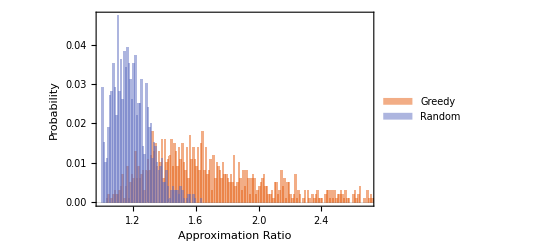

```mathematica
Histogram[{res[[1]]/res[[2]],res[[1]]/res[[3]]},300,"Probability",Frame->True,FrameLabel->{"Approximation Ratio","Probability"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",ChartLegends->Placed[{"Greedy","Random"},{.7,.8}]]
```

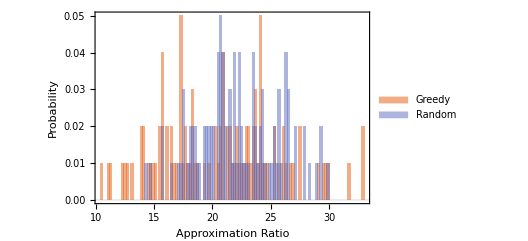
```mathematica
-Graphics-//Compress
```

```mathematica
adj=Transpose[Join[(Join[ConstantArray[∞,m],#1]&)/@Transpose[Ramp[dis-w]],Zero[n,m+n]]/.{0.->∞}];g=WeightedAdjacencyGraph[Join[organs,patients],adj];flow=FindMaximumFlow[g,patients,organs,"OptimumFlowData",VertexCapacity->ConstantArray[1,n+m]];mm=NormalEdgeForm/@flow["EdgeList"];wait=w⟦mm⟦All,1⟧⟧;gains=f/@mm-wait;ord=Reverse[Ordering[gains]];alc=ConstantArray[0,Min[m,n]];((alc=PlaceAtLast[mm⟦#1⟧,alc,wait⟦#1⟧])&)/@ord;alc=alc/.{0->Nothing};greedy=Goal[w,p,alc];rdnSol=Max[Table[SampleGoal[w,p,o],(n+m)^2]];{greedy,rdnSol}
```

{28.3489,35.3816}

```mathematica
n=30;
m=20;
p=Range[n];
o=Range[m];

w=RandomVariate[PoissonDistribution[10],n];pZ=RandomVariate[NormalDistribution[0,10],n];oZ=RandomVariate[NormalDistribution[0,10],m];dis=5 Ramp[DistanceMatrix[pZ,oZ]-10];

T = Min[m, n];
var[i_,j_, t_] := Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t];
waitConstr[w_, i_] :=  Table[Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t] == 0, {j, m}, {t, w+1, T}] // Flatten;
obj1 = Table[-dis[[i,j]]*var[i,j,t], {i,  n}, {j,  m}, {t, T}] // Flatten // Total;
obj2 = Table[-w[[i]] * (1 - (Table[var[i,j,t], {j, m},{t, T}] // Flatten // Total )), {i, n}]  // Total;
obj = obj1 + obj2;
constr = Table[(Flatten[Table[var[i,j,t], {j, m},{t, T}] ] // Total) <= 1, {i, n}];
constr2 = Table[( Flatten[Table[var[i,j,t], {i, n}, {t, T}]] //Total) <= 1, {j, m}];
constr3 = Table[ (Flatten[Table[var[i,j,t], {i, n}, {j, m}]] //Total)<= 1, {t, T}];
constr4 = Table[var[i,j,t] >= 0, {i, n}, {j, m}, {t, T}] // Flatten;
constr5 = waitConstr[#[[1]], #[[2]]]&/@Transpose[{w, p}] // Flatten;
res = LinearOptimization[obj1+obj2, constr~Join~constr2~Join~constr3~Join~constr4~Join~constr5, Table[var[i,j,t]∈ Integers, {i, n}, {j, m}, {t, T}]//Flatten];
SplitRes[s_]:= ToString@s// StringSplit[#, "x"]& // StringSplit[#, "d"]& //ToExpression// Flatten;
ExtractAllocation[res_]:=SortBy[SplitRes[#[[1]]] & /@ Select[res, (#[[2]] == 1&)], Last];
-(obj/.res)/ n//AbsoluteTiming
```

51.8145

```mathematica
Sim2[λ_]:=Module[{},
w=RandomVariate[PoissonDistribution[λ],n];pZ=RandomVariate[NormalDistribution[0,10],n];oZ=RandomVariate[NormalDistribution[0,10],m];dis=5 Ramp[DistanceMatrix[pZ,oZ]-10];adj=Transpose[Join[(Join[ConstantArray[∞,m],#1]&)/@Transpose[dis],Zero[n,m+n]]/.{0.->∞}];g=WeightedAdjacencyGraph[Join[organs,patients],adj];flow=FindMaximumFlow[g,patients,organs,"OptimumFlowData",VertexCapacity->ConstantArray[1,n+m]];mm=NormalEdgeForm/@flow["EdgeList"];wait=w⟦mm⟦All,1⟧⟧;gains=f/@mm-wait;ord=Reverse[Ordering[gains]];alc=ConstantArray[0,Min[m,n]];((alc=PlaceAtLast[mm⟦#1⟧,alc,wait⟦#1⟧])&)/@ord;alc=alc/.{0->Nothing};greedy=Goal[w,p,alc];rdnSol=Max[Table[SampleGoal[w,p,o],(n+m)]];
greedy-rdnSol
]
```

```mathematica
$KernelCount
```

0

```mathematica
n=10;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res10=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],1000];

n=20;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res20=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],1000];

n=30;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res30=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],1000];

n=40;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res40=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],1000];

n=50;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res50=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],1000];
```

```mathematica
Range[10,50,10]
```

{10,20,30,40,50}

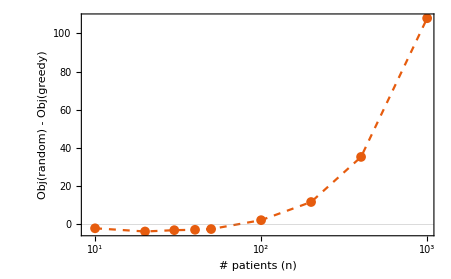

```mathematica
ListLinePlot[({{10,20,30,40,50,100,200,400,1000},-(Mean/@{res10,res20,res30,res40,res50,res100,res200,res400,res1000})}ᵀ),PlotRange->Full,Frame->True,
ScalingFunctions->{"Log10",Automatic},FrameLabel->{"# patients (n)","Obj(random) - Obj(greedy)"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",PlotMarkers->{Automatic, 10},PlotStyle->Dashed]
```

```mathematica
n=1000;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res1000=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],10];
```

```mathematica
res50//Mean
```

2.39567

```mathematica
n=400;
m=n;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
res400=ResourceFunction["MonitorProgress"]@Table[Sim2[Floor[n/3]],50];
```